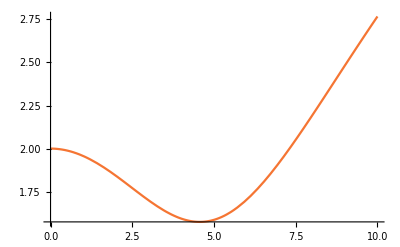

```mathematica
Uy[ω_]:=Sqrt[I ω] ((1+ Sqrt[I ω] Coth[Sqrt[I ω]])*Coth[Sqrt[I ω]]-Sqrt[I ω])
AbsArgPlot[Uy[ω],{ω,0,10}]
```

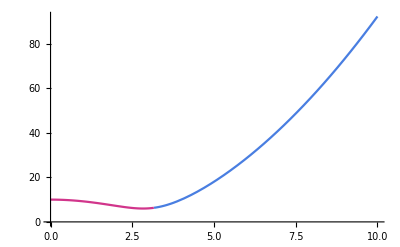

```mathematica
AbsArgPlot[1/σ[ω,3],{ω,0,10}]
```

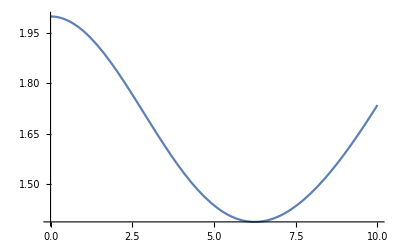

```mathematica
Plot[Re[Uy[ω]],{ω,0,10}]
```

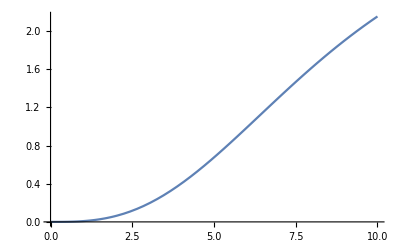

```mathematica
Plot[Im[Uy[ω]],{ω,0,10}]
```

1/(√(4 ω^2+(1-ω^2+ω0^2)^2))

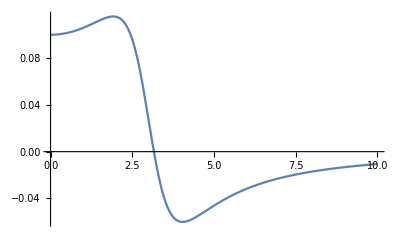

```mathematica
Plot[Re[σ[ω,3]],{ω,0,10}]
```

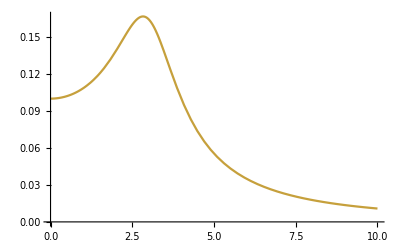

```mathematica
AbsArgPlot[{σ[ω,3],{ω,0,10}]
```

```mathematica
σ2[ω_,ω0_,τ_]:=1/((1- I ω τ)^2+(ω0 τ)^2)
ComplexExpand[Abs[σ2[ω,ω0,τ]]]
```

1/(√(4 τ^2 ω^2+(1-τ^2 ω^2+τ^2 ω0^2)^2))